```mathematica
Quit[]
```

```mathematica
ClearAll["Global`*"]
```

### Pre-homeostasis ODEs

#### Lagrangian formulation

```mathematica
RodOdeLagrangian[R:{__?NumericQ}]:=Block[
{Sol,S,s,nx,ny,x,y,θ,m},
Sol=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S]*(x[S]-px[S]),
ny'[S]==k γ[S](y[S]-py[S]),
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]]),
x[0]==0,y[0]==R[[2]],θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x[S],y[S],θ[S],s[S],nx[S],ny[S],m[S]},{S,0,L/2}][[1]];
{x[S]-L/2,y[S],θ[S]}/.Sol/.S->L/2
];

EquilSolLagrangian[R_]:=NDSolve[
{x'[S]==γ[S]Cos[θ[S]],
y'[S]==γ[S]Sin[θ[S]],
s'[S]==γ[S],
nx'[S]==k γ[S](x[S]-px[S]),
ny'[S]==k γ[S](y[S]-py[S]),
θ'[S]==EB[s[S]]γ[S]m[S],
m'[S]==γ[S](nx[S]*Sin[θ[S]]-ny[S]Cos[θ[S]]),
x[0]==0,y[0]==R[[2]],θ[0]==0,s[0]==0,nx[0]==R[[1]],ny[0]==0,m[0]==R[[3]]},
{x,y,θ,s,m,nx,ny},{S,0,L/2}][[1]];
```

## Obtain pre-homeostasis solutions

```mathematica
(* Get the data for the initial solution *)
initSolData = Import["~/Documents/MorphoCrypt/Data/planarmorphorodsinextkf0p01L1sol_1"];
y0=initSolData[[300]][[4]];
nx0=initSolData[[300]][[5]];
m0=initSolData[[300]][[8]];
R0 = {nx0, y0, m0};
```

```mathematica
W=Function[s,Exp[-s^2/(.16)^2]];
```

First simulate in the Lagrangian frame for Wnt-based growth.

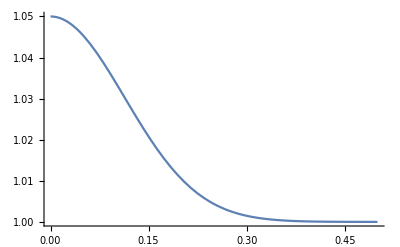

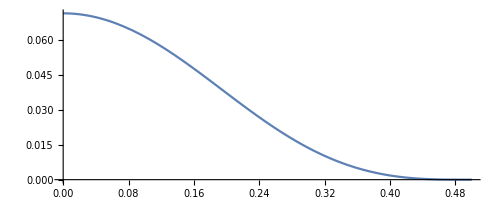

```mathematica
Clear[γ,R,SolLagrangian,solLagrangian,EB,px,py];

(* parameters *)
w = 0.010;
L0=0.125;
h = 0.015;
kf =0.01;
(*Q = 0.1;
n = 2;*)

k=(12*kf*L0^4)/(w*h^3);
dt=0.05;
dth = dt; (* initialising successful step size *)
δ=0.02;
L=1;
η=10;
γ[S_]=1+dt*W[S];
px[S_]:=S;
py[S_]:=0;
EB[s_]:=1;
SolLagrangian=FindRoot[RodOdeLagrangian[R],{R,R0}];
Plot[γ[S],{S,0,1/2}]
ParametricPlot[Evaluate[{x[S],y[S]}/.EquilSolLagrangian[R/.SolLagrangian[[1]]]],{S,0,L/2}]
```

```mathematica
(* first step *)
grs={};
γ[S_]=1+dt*W[S];
SolLagrangian=FindRoot[RodOdeLagrangian[R],{R,R/.SolLagrangian}];
solLagrangian=EquilSolLagrangian[R/.SolLagrangian[[1]]];
rs=R/.SolLagrangian;
AppendTo[grs,{γ[S],L,EB[s],k,rs,solLagrangian,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.solLagrangian,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.solLagrangian,{S,0,L/2}];
```

```mathematica
(* second step *)
Clear[γOld,γNew];
γOld=γ;
γNew=FunctionInterpolation[Evaluate[Table[D[γOld[S]*(1+dt*W[s[S]])/.solLagrangian,{S,k}],{k, 0, 1}]],{S, 0, 1/2}];

γ=γNew;
SolLagrangian=FindRoot[RodOdeLagrangian[R],{R,R/.SolLagrangian}];
solLagrangian=EquilSolLagrangian[R/.SolLagrangian[[1]]];
re=R/.SolLagrangian[[1]];
AppendTo[grs,{γ[S],L,EB[s],k,rs,solLagrangian,px,py}];
(* update foundation *)
Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.solLagrangian,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.solLagrangian,{S,0,L/2}];
```

```mathematica
(* Iterate the solution over time now *) 
flag=0;
FailCount=0;
TOL=10^-6;
MaxDt=0.45;
MaxFails=60;

P1=ParametricPlot[Evaluate[{x[S],y[S]}/.solLagrangian,{S,0,L/2}]];
P2=Plot[nx[S]/.solLagrangian,{S,0,L/2}];

J1 = CreateWindow[DocumentNotebook[P1],WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
J2 = CreateWindow[DocumentNotebook[P2],WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];

(*Dynamic[Refresh[Show[P,PlotRange->All],UpdateInterval->$TimeUnit,TrackedSymbols->{P}],SynchronousUpdating->True]*)
While[flag==0,
t = (re - rs);
Clear[γOld,γNew];
γOld=γ;
γNew=FunctionInterpolation[Evaluate[Table[D[γOld[S]*(1+dt*W[s[S]])/.solLagrangian,{S,k}],{k, 0, 1}]],{S, 0, 1/2}];

γ=γNew;
SolLagrangian=Quiet[Reap[FindRoot[RodOdeLagrangian[R],{R,re+dt/dth*t}, StepMonitor :> Sow[R]]]];
Err=Norm[RodOdeLagrangian[R/.SolLagrangian[[1]]]];
If[Err > TOL, 
(* reject solution, decrease step size *)
FailCount = FailCount + 1; 
Clear[γ];
γ = γOld;
dt = 0.5 dt; Print[dt];If[FailCount == MaxFails, flag = 1,];,

(* else accept solution, store data, update foundation *)
solLagrangian=EquilSolLagrangian[R/.SolLagrangian[[1]]];
rs = re;
re = R/.SolLagrangian[[1]];
AppendTo[grs,{γ[S],L,EB[s],k,rs,solLagrangian,px,py}];

Px=px;
Py=py;
px=FunctionInterpolation[(η*dt*x[S]+(1-η*dt)Px[S])/.solLagrangian,{S,0,L/2}];
py=FunctionInterpolation[(η*dt*y[S]+(1-η*dt)Py[S])/.solLagrangian,{S,0,L/2}];
(* update successful step size *)
dth=dt;

(* live plotting *)
P1=ParametricPlot[Evaluate[{x[S],y[S]}/.solLagrangian,{S,0,L/2}]];
P2=Plot[(nx[S]*Cos[θ[S]]+ny[S]*Sin[θ[S]])/.solLagrangian,{S,0,L/2},PlotRange-> {-100, 0}];
CreateWindow[DocumentNotebook[P1],J1,WindowMargins -> {{50, Automatic}, {Automatic, 0}}, WindowSize -> 500];
 CreateWindow[DocumentNotebook[P2],J2,WindowMargins -> {{600, Automatic}, {Automatic, 0}}, WindowSize -> 500];
(*FinishDynamic[]*);

(* criteria to increase step size, based on number of steps to convergence of FindRoot *)steps = Length[SolLagrangian[[2]][[1]]];
If[steps < 4, dt = Min[1.25*dt, MaxDt]; Print[dt],];
];

];
```

0.0625

0.03125

0.015625

0.0195313

0.0244141

0.0305176

0.0152588

0.00762939

0.00953674

0.0119209

0.0149012

0.0186265

0.0232831

0.0291038

0.0363798

0.0454747

0.0227374

0.0284217

0.0355271

0.0177636

0.0222045

0.0277556

0.0346945

0.0433681

0.021684

0.010842

0.00542101

0.00271051

0.00338813

0.00169407

0.000847033

0.000423516

0.000529396

0.000661744

0.000330872

0.00041359

0.000206795

0.000103398

0.000129247

0.000161559

0.0000807794

0.0000403897

0.0000201948

0.0000100974

5.04871×10^-6

6.31089×10^-6

3.15544×10^-6

1.57772×10^-6

1.97215×10^-6

9.86076×10^-7

1.2326×10^-6

1.54074×10^-6

1.92593×10^-6

2.40741×10^-6

3.00927×10^-6

3.76158×10^-6

4.70198×10^-6

5.87747×10^-6

7.34684×10^-6

9.18355×10^-6

0.0000114794

0.0000143493

0.0000179366

0.0000224208

0.000028026

0.0000350325

0.0000437906

0.0000547382

0.0000684228

0.0000342114

0.0000171057

8.55285×10^-6

4.27642×10^-6

2.13821×10^-6

1.06911×10^-6

5.34553×10^-7

2.67276×10^-7

1.33638×10^-7

1.67048×10^-7

8.35239×10^-8

4.17619×10^-8

2.0881×10^-8

1.04405×10^-8

1.30506×10^-8

1.63133×10^-8

2.03916×10^-8

1.01958×10^-8

5.09789×10^-9

2.54895×10^-9

1.27447×10^-9

$Aborted

0.00117549

$Aborted

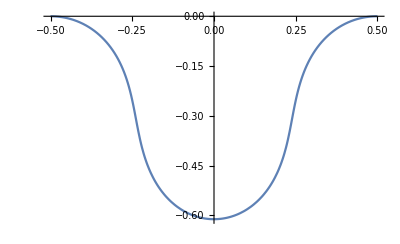

```mathematica
ParametricPlot[{{x[S],-y[S]},{-x[S], -y[S]}}/.solLagrangian,{S, 0, 1/2},PlotRange-> Full]
```

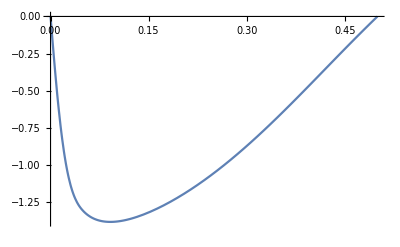

```mathematica
Plot[(θ[S])/.solLagrangian,{S, 0, 0.5},PlotRange-> Full]
```

```mathematica
WntScale=NIntegrate[W[S],{S, 0, 0.5}]
```

0.141795

```mathematica
WntScale=NIntegrate[W[s],{s, 0, l}]
```

Check the homogeneous stress

We need to define the homeostatic shape, (x[s], y[s]), which are defined by θ[s] and subsequently, m=θ’[s].

```mathematica
currentLength=s[0.5]/.solLagrangian
```

0.867207

```mathematica
S0Mesh = Range[0, 0.5, 0.005];
```

```mathematica
xHom=Interpolation[Table[{s[S0Mesh[[i]]],x[S0Mesh[[i]]]}/.solLagrangian,{i, 1, Length[S0Mesh]}]];
yHom=Interpolation[Table[{s[S0Mesh[[i]]],y[S0Mesh[[i]]]}/.solLagrangian,{i, 1, Length[S0Mesh]}]];
θHom=Interpolation[Table[{s[S0Mesh[[i]]],θ[S0Mesh[[i]]]}/.solLagrangian,{i, 1, Length[S0Mesh]}]];
mHom=Interpolation[Table[{s[S0Mesh[[i]]],m[S0Mesh[[i]]]}/.solLagrangian,{i, 1, Length[S0Mesh]}]];
```

```mathematica
nx[S]*Cos[θ[S]]+ny[S]*Sin[θ[S]]/.solLagrangian
```

Cos[InterpolatingFunction[{{0., 0.5}}, <>][S]] InterpolatingFunction[{{0., 0.5}}, <>][S]+Sin[InterpolatingFunction[{{0., 0.5}}, <>][S]] InterpolatingFunction[{{0., 0.5}}, <>][S]

```mathematica
h^2/(12*L0^2)
```

0.0012

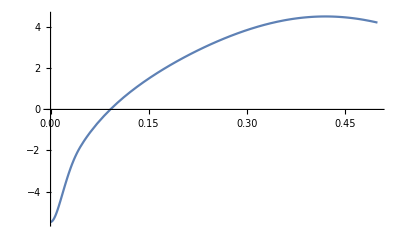

```mathematica
Plot[{m[S]/.solLagrangian},{S, 0, 0.5}]
```

## Homeostasis ODEs

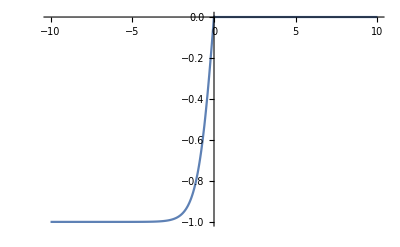

```mathematica
f=Function[m,Tanh[m]*1/2(1+Tanh[-50m])];
Plot[f[ns],{ns,-10,10}]
```

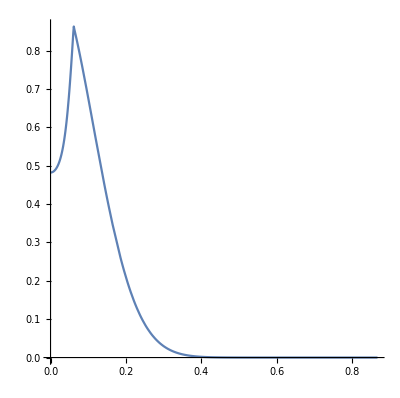

```mathematica
ParametricPlot[{s[S]/.solLagrangian,W[s[S]/.solLagrangian]+0.6*W[s[S]/.solLagrangian]*f[((nx[S]*Cos[θ[S]]+ny[S]*Sin[θ[S]])/.solLagrangian)+ 25]/.ParSubs},{S, 0, 1/2},PlotRange-> Full]
```

```mathematica
nx[0]/.solLagrangian
```

-26.3036

```mathematica
Clear[k];
```

```mathematica
ParSubs={k->1000,μ->0.6,ρ->1,ns->-25,n0->-26.5};
AppendTo[ParSubs, β->(W[0]+μ*Tanh[(n0-ns)]*W[0])/.ParSubs];
(W[0]+μ*Tanh[(n0-ns)])/.ParSubs
```

0.456911

```mathematica
ParSubs
```

{k→1000,μ→0.5,ρ→10,ns→-26.5,n0→-25,β→1.45257}

```mathematica
Plot[D[θHom[s],s],{s, eps, l}]
```

General::ivar: 0.000117714 is not a valid variable.

General::ivar: 0.0178138 is not a valid variable.

General::ivar: 0.0355098 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

-Graphics-

```mathematica
Clear[px, py, k];
```

```mathematica
h^2/L^2
```

0.000225

```mathematica
eps=0.0001;
InextensibleHomeostasisSol=NDSolve[{v'[s]==-(W[s]+μ f[nx[s]*Cos[θHom[s]]+ny[s]*Sin[θHom[s]]-ns]*W[s]),
nx'[s]==k *(xHom[s]-px[s]),
ny'[s]==k*(yHom[s]-py[s]),
px'[s]==ρ (px[s]-xHom[s])/v[s],
py'[s]==ρ*(py[s]-yHom[s])/v[s],
II'[s]==(β-(W[s]+μ f[nx[s]*Cos[θHom[s]]+ny[s]*Sin[θHom[s]]-ns]))/v[s],
Sh'[s]==Exp[-II[s]],
nx[eps]==n0,
ny[eps]==0,
px[eps]==eps*ρ/(ρ+(W[0]+μ*f[n0-ns])),
py[eps]==yHom[eps],
v[eps]==-eps*(W[0]+μ*f[n0-ns]),
II[eps]==0,Sh[eps]==eps}/.ParSubs,{nx, ny, px, py, v,II,Sh},{s, eps, currentLength},MaxStepSize-> 0.005,Method-> "StiffnessSwitching"][[1]];
Es = 0.001;
ExtensibleHomeostasisSol=NDSolve[{v'[s]==(Es*(k *(xHom[s]-px[s])*Cos[θHom[s]]+k*(yHom[s]-py[s])*Sin[θHom[s]]+(mHom[s]/(1+Es*(nx[s]*Cos[θHom[s]]+ny[s]*Sin[θHom[s]])))*(ny[s]*Cos[θHom[s]]-nx[s]*Sin[θHom[s]]))*v[s])/(1+Es*(nx[s]*Cos[θHom[s]]+ny[s]*Sin[θHom[s]]))-(W[s]+μ f[nx[s]*Cos[θHom[s]]+ny[s]*Sin[θHom[s]]-ns]*W[s]),
nx'[s]==k *(xHom[s]-px[s]),
ny'[s]==k*(yHom[s]-py[s]),
px'[s]==ρ (px[s]-xHom[s])/v[s],
py'[s]==ρ*(py[s]-yHom[s])/v[s],
II'[s]==(β-(W[s]+μ f[nx[s]*Cos[θHom[s]]+ny[s]*Sin[θHom[s]]-ns]))/v[s],
Sh'[s]==Exp[-II[s]],
nx[eps]==n0,
ny[eps]==0,
px[eps]==eps*ρ/(ρ+(W[0]+μ*f[n0-ns])),
py[eps]==yHom[eps],
v[eps]==-eps*(W[0]+μ*f[n0-ns]),
II[eps]==0,Sh[eps]==eps}/.ParSubs,{nx, ny, px, py, v,II,Sh},{s, eps, currentLength},Method-> "StiffnessSwitching"][[1]];
```

```mathematica
Clear[γ,S0]
```

```mathematica
γFun=Function[{s,t},A0 Exp[β t]Exp[II[s]]];
S0Fun=Function[{s,t},Exp[-β t]Sh[s]/A0];
```

We choose the constant so that Lmu = 1/2 at t=0

```mathematica
A0=2*Sh[s]/.InextensibleHomeostasisSol/.s->currentLength
```

3.43682

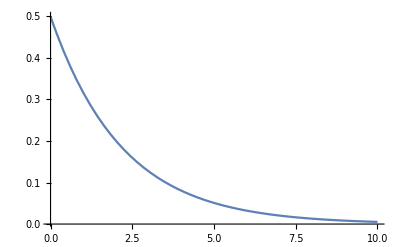

```mathematica
Lmu=Function[t,S0Fun[s,t]/.InextensibleHomeostasisSol/.ParSubs/.s->currentLength];
Plot[Lmu[t],{t,0,10},PlotRange-> Full]
```

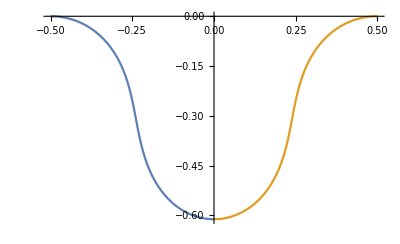

```mathematica
ParametricPlot[{{-xHom[s],-yHom[s]},{xHom[s],-yHom[s]},{-xHom[0.2],-yHom[0.2]},{xHom[0.2],-yHom[0.2]}},{s, 0, currentLength}]
```

```mathematica
ns/.ParSubs
```

-26.5

```mathematica
nx[eps]/.InextensibleHomeostasisSol
```

{-25.}

```mathematica
l=currentLength;
```

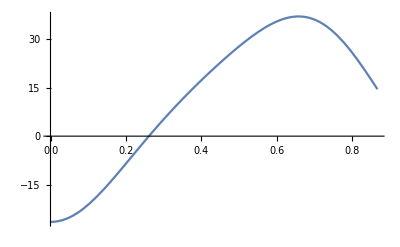

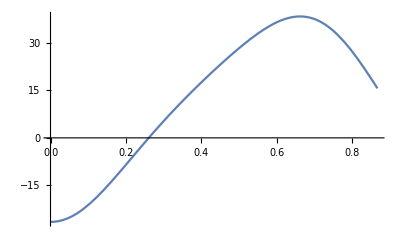

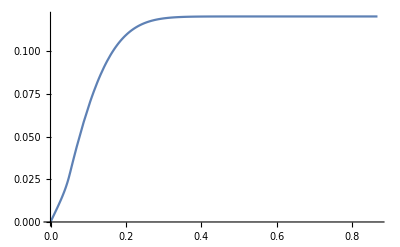

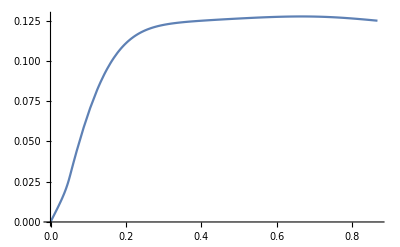

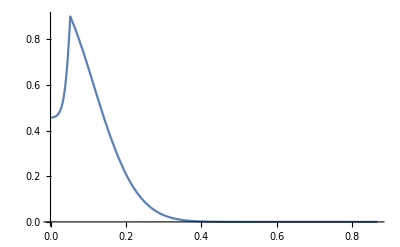

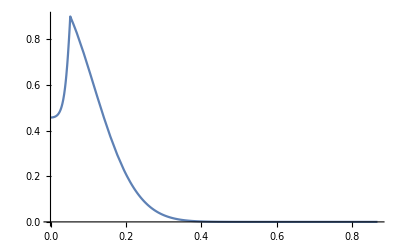

```mathematica
Plot[(nx[s]*Cos[θHom[s]]+ny[s]*Sin[θHom[s]])/.InextensibleHomeostasisSol,{s, eps, l}]
Plot[(nx[s]*Cos[θHom[s]]+ny[s]*Sin[θHom[s]])/.ExtensibleHomeostasisSol,{s, eps, l}]
Plot[-v[s]/.InextensibleHomeostasisSol,{s, eps, l},PlotRange-> Full]
Plot[-v[s]/.ExtensibleHomeostasisSol,{s, eps, l},PlotRange-> Full]
Plot[ W[s]+μ*f[nx[s]*Cos[θHom[s]]+ny[s]*Sin[θHom[s]]-ns]/.InextensibleHomeostasisSol/.ParSubs,{s, eps, l}]
Plot[ W[s]+μ*f[nx[s]*Cos[θHom[s]]+ny[s]*Sin[θHom[s]]-ns]/.ExtensibleHomeostasisSol/.ParSubs,{s, eps, l}]
```

Define the various initial profiles, as obtained by the homeostasis equations. We define the solutions at s = 0.

```mathematica
l=currentLength;
```

```mathematica
sMesh=Range[eps,l, 150*eps];
Length[sMesh]
```

598

```mathematica
px[eps]/.InextensibleHomeostasisSol
```

9.60796×10^-6

```mathematica
yHom[0]
```

0.638409

```mathematica
f
```

Function[m,1/2 Tanh[m] (1+Tanh[-50 m])]

```mathematica
S0Init=Interpolation[Join[{{0, 0}}, Table[{sMesh[[i]],S0Fun[sMesh[[i]],0]/.InextensibleHomeostasisSol},{i, 1, Length[sMesh]}],{{l, 1/2}}]];
γInit=Interpolation[Join[{{0, A0}}, Table[{sMesh[[i]],γFun[sMesh[[i]],0]/.InextensibleHomeostasisSol},{i, 1, Length[sMesh]}],{{l,γFun[l,0]/.InextensibleHomeostasisSol}}]];
pxHom=Interpolation[Join[{{0, 0}}, Table[{sMesh[[i]],px[sMesh[[i]]]/.InextensibleHomeostasisSol},{i, 1, Length[sMesh]}],{{l,px[l]/.InextensibleHomeostasisSol}}]];
pyHom=Interpolation[Join[{{0, yHom[0]}}, Table[{sMesh[[i]],py[sMesh[[i]]]/.InextensibleHomeostasisSol},{i, 1, Length[sMesh]}],{{l,py[l]/.InextensibleHomeostasisSol}}]];
nxHom=Interpolation[Join[{{0, n0/.ParSubs}}, Table[{sMesh[[i]],nx[sMesh[[i]]]/.InextensibleHomeostasisSol},{i, 1, Length[sMesh]}],{{l,nx[l]/.InextensibleHomeostasisSol}}]];
nyHom=Interpolation[Join[{{0, 0}}, Table[{sMesh[[i]],ny[sMesh[[i]]]/.InextensibleHomeostasisSol},{i, 1, Length[sMesh]}],{{l,ny[l]/.InextensibleHomeostasisSol}}]];
```

Let’s try verifying this in 2D.

```mathematica
W[s]+μ*f[nx[s,t]*Cos[θ[s,t]]+ny[s,t]*Sin[θ[s,t]]-ns]
```

ⅇ^(-6.25 s^2)-1/2 μ Tanh[ns-Cos[θ[s,t]] nx[s,t]-ny[s,t] Sin[θ[s,t]]] (1-Tanh[50 (-ns+Cos[θ[s,t]] nx[s,t]+ny[s,t] Sin[θ[s,t]])])

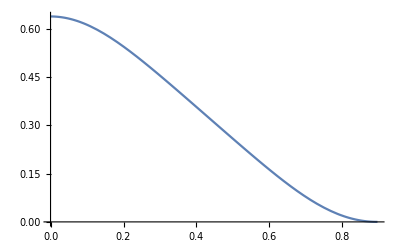

```mathematica
Plot[yHom[s],{s, 0, l}]
```

```mathematica
f
```

Function[m,1/2 Tanh[m] (1+Tanh[-50 m])]

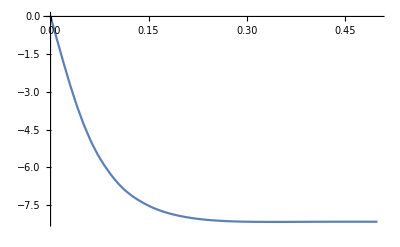

```mathematica
Plot[-ny[S]/.solLagrangian,{S, 0, 1/2},PlotRange-> Full]
```

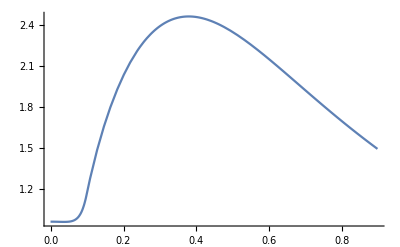

```mathematica
Plot[γInit[s],{s, 0, l}]
```

```mathematica
f
```

Function[m,1/2 Tanh[m] (1+Tanh[-50 m])]

```mathematica
FullInextensibleHomeostasis2DSol = NDSolve[{D[S0[s, t],s]==1/γ[s,t],
D[x[s,t],s]==Cos[θ[s,t]],
D[y[s,t],s]==Sin[θ[s,t]],
D[nx[s, t], s]==k*(x[s,t]-px[s, t]),
D[ny[s, t], s]==k*(y[s,t]-py[s, t]),
D[θ[s,t],s]==m[s,t],
D[m[s,t],s]== nx[s,t]*Sin[θ[s,t]]-ny[s,t]*Cos[θ[s,t]],
D[γ[s,t],t]==γ[s,t]*(W[s]+μ*1/2 Tanh[nx[s,t]*Cos[θ[s,t]]+ny[s,t]*Sin[θ[s,t]]-ns]*(1+Tanh[-50 *(nx[s,t]*Cos[θ[s,t]]+ny[s,t]*Sin[θ[s,t]]-ns)]))+γ[s,t]*D[γ[s,t], s]*D[S0[s, t], t],
D[px[s, t], t]==ρ*(x[s,t]-px[s, t])+γ[s,t]*D[px[s,t], s]*D[S0[s, t], t],
D[py[s, t], t]==ρ*(y[s,t]-py[s, t])+γ[s,t]*D[py[s,t], s]*D[S0[s, t], t],
S0[0,t]==0,S0[currentLength,t]==Lmu[t],x[0, t]==0, x[currentLength,t]==0.5, y[currentLength,t]==0,ny[0,t]==0, θ[0, t]==0, θ[currentLength,t]==0,γ[s,0]==γInit[s],S0[s,0]==S0Init[s],x[s,0]==xHom[s],y[s,0]==yHom[s], nx[s,0]==nxHom[s],ny[s,0]==nyHom[s],px[s, 0]==pxHom[s],py[s,0]==pyHom[s],θ[s,0]==θHom[s],m[s,0]==mHom[s]}/.ParSubs,{S0,γ,x,y,nx,ny, px,py,θ,m},{s,0,currentLength},{t,0,4},Method->{"IndexReduction"->Automatic}][[1]];
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

NDSolve::nlnum1: The function value 0.961045934943242`  - 1.` TagBox[InterpolatingFunction[{{0.`, 0.8959206840006635`}}, {4, 7, 0, {600}, {4}, 0, 0, 0, 0, Automatic, {}, {}, False}, « 1 », {Developer`PackedArrayForm, {0, 1, 2, « 46 », 49, « 551 »}, {0.961045934943242`, 0.961045934943242`, 0.9610407545917243`, 0.9610253921927595`, 0.9609999709745142`, 0.9609646972497743`, 0.9609198631520341`, 0.9608658456939252`, 0.9608031120672956`, « 33 », 0.9676917221589266`, 0.969235685929116`, 0.9709945118695097`, 0.9729927909041419`, 0.9752558657921666`, 0.9778132188720178`, 0.9806973094468253`, 0.9839416379928356`, « 550 »}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]][s]« 49 »« 200 » is not a list of numbers with dimensions {250} when the arguments are {0., « 19 », {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}}.

NDSolve::nlnum1: The function value {Hold[{{-5.35717, -5.29835, -5.12452, -4.84295, -4.46537, -4.00669, -3.48312, -2.91013, -2.30112, -1.66705, -1.01717, -0.359734, 0.297605, 0.947319, 1.58044, 2.18622, 2.75163, 3.2612, 3.69779, 4.04382, 4.28326, 4.40377, 4.39868, 4.26814, 4.01902} + {5.35717, « 23 », -« 18 »}, « 9 »}, {« 1 »}]} is not a list of numbers with dimensions {1} when the arguments are {0., « 19 », {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}}.

NDSolve::icfail: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Part::partw: Part 1 of {} does not exist.

```mathematica
(*FullInextensibleHomeostasis2DSol = NDSolve[{D[S0[s, t],s]==1/γ[s,t],
D[x[s,t],s]==Cos[θ[s,t]],
D[y[s,t],s]==Sin[θ[s,t]],
D[nx[s, t], s]==k*(x[s,t]-px[s, t]),
D[ny[s, t], s]==k*(y[s,t]-py[s, t]),
D[θ[s,t],s]==m[s,t],
D[m[s,t],s]== nx[s,t]*Sin[θ[s,t]]-ny[s,t]*Cos[θ[s,t]],
D[γ[s,t],t]==γ[s,t]*(W[s]+μ*1/2 Tanh[nx[s,t]*Cos[θ[s,t]]+ny[s,t]*Sin[θ[s,t]]-ns]*(1+Tanh[-50 *(nx[s,t]*Cos[θ[s,t]]+ny[s,t]*Sin[θ[s,t]]-ns)]))+γ[s,t]*D[γ[s,t], s]*D[S0[s, t], t],
D[px[s, t], t]==ρ*(x[s,t]-px[s, t])+γ[s,t]*D[px[s,t], s]*D[S0[s, t], t],
D[py[s, t], t]==ρ*(y[s,t]-py[s, t])+γ[s,t]*D[py[s,t], s]*D[S0[s, t], t],
S0[0,t]==0,S0[currentLength,t]==Lmu[t],x[0, t]==0, x[currentLength,t]==0.5, y[currentLength,t]==0,ny[0,t]==0, θ[0, t]==0, θ[currentLength,t]==0,γ[s,0]==γInit[s],S0[s,0]==S0Init[s],x[s,0]==xHom[s],y[s,0]==yHom[s], nx[s,0]==nxHom[s],ny[s,0]==nyHom[s],px[s, 0]==pxHom[s],py[s,0]==pyHom[s],θ[s,0]==θHom[s],m[s,0]==mHom[s]}/.ParSubs,{S0,γ,x,y,nx,ny, px,py,θ,m},{s,0,currentLength},{t,0,1},Method->{"IndexReduction"->Automatic}][[1]];*)
```

NDSolve::pdord: Some of the functions have zero differential order, so the equations will be solved as a system of differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable s. Artificial boundary effects may be present in the solution.

NDSolve::nlnum1: The function value 0.961045934943242`  - 1.` TagBox[InterpolatingFunction[{{0.`, 0.8959206840006635`}}, {4, 7, 0, {600}, {4}, 0, 0, 0, 0, Automatic, {}, {}, False}, « 1 », {Developer`PackedArrayForm, {0, 1, 2, « 46 », 49, « 551 »}, {0.961045934943242`, 0.961045934943242`, 0.9610407545917243`, 0.9610253921927595`, 0.9609999709745142`, 0.9609646972497743`, 0.9609198631520341`, 0.9608658456939252`, 0.9608031120672956`, « 33 », 0.9676917221589266`, 0.969235685929116`, 0.9709945118695097`, 0.9729927909041419`, 0.9752558657921666`, 0.9778132188720178`, 0.9806973094468253`, 0.9839416379928356`, « 550 »}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]][s]« 49 »« 200 » is not a list of numbers with dimensions {250} when the arguments are {0., « 19 », {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}}.

NDSolve::nlnum1: The function value {Hold[{{-5.35717, -5.29835, -5.12452, -4.84295, -4.46537, -4.00669, -3.48312, -2.91013, -2.30112, -1.66705, -1.01717, -0.359734, 0.297605, 0.947319, 1.58044, 2.18622, 2.75163, 3.2612, 3.69779, 4.04382, 4.28326, 4.40377, 4.39868, 4.26814, 4.01902} + {5.35717, « 23 », -« 18 »}, « 9 »}, {« 1 »}]} is not a list of numbers with dimensions {1} when the arguments are {0., « 19 », {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0.}}.

NDSolve::icfail: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

Part::partw: Part 1 of {} does not exist.

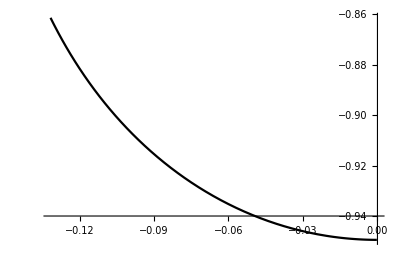

```mathematica
ParametricPlot[{-x[S],-y[S]}/.solLagrangian,{S,eps, LLmu},PlotStyle->Black]
```

```mathematica
ss
```

{}

```mathematica
SS0=Range[.01,.04,.01];
ss0 = Range[.01,.04,.01];
TT=Range[0.1,10,.1];
(*TT = 0.1;*)
Plots={};
Colors={Blue,Green,Yellow,Red};
For[j=1,j≤Length[TT],j++,
tt=TT[[j]]; (* the time *)
LLmu=Lmu[t]/.InextensibleHomeostasisSol/.ParSubs/.t->tt;
ss={};
xs={};
ys={};
For[i=1,i≤Length[SS0],i++,
If[LLmu>SS0[[i]],
sSol=FindRoot[SS0[[i]]-(S0[s,t]/.InextensibleHomeostasisSol/.ParSubs/.t->tt),{s,0.2,eps,1}][[1]];
AppendTo[ss, s/.sSol];
AppendTo[xs,xHom[s/.sSol]];
AppendTo[ys,yHom[s/.sSol]];,
];];
(*(* foundation *)
ppx={};ppy={};
For[i=1,i≤Length[ss],i++,
AppendTo[ppx,px[s]/.InextensibleHomeostasisSol/.s->ss[[i]]];
AppendTo[ppy,py[s]/.InextensibleHomeostasisSol/.s->ss[[i]]];];*)

AppendTo[Plots,Show[
(* initial configuration - past Lmu is dashed *)
ParametricPlot[{-x[S],-y[S]}/.solLagrangian,{S,0, LLmu},PlotStyle->Black,PlotRange->{{-0.5, 2},{-1.1,.1}}],
ParametricPlot[{x[S],-y[S]}/.solLagrangian,{S,0,LLmu},PlotStyle->Black,PlotRange->{{-0.5, 2},{-1.1,.1}}],
ParametricPlot[{x[S],-y[S]}/.solLagrangian,{S,LLmu,1/2},PlotStyle->{Black,Dashed},PlotRange->{{-0.5, 2},{-1.1,.1}}],
ParametricPlot[{-x[S],-y[S]}/.solLagrangian,{S,LLmu,1/2},PlotStyle->{Black,Dashed},PlotRange->{{-0.5, 2},{-1.1,.1}}],
(* and a small disk at Lmu *)
Graphics[{Black,Disk[{x[LLmu],-y[LLmu]}/.solLagrangian,0.01]}],
Graphics[{Black,Disk[{-x[LLmu],-y[LLmu]}/.solLagrangian,0.01]}],(*
Table[Graphics[{Colors[[k]],Disk[{x[SS0[[k]]],-y[SS0[[k]]]}/.solLagrangian,0.04]}],{k,1,Length[SS0]}],
Table[Graphics[{Colors[[k]],Disk[{-x[SS0[[k]]],-y[SS0[[k]]]}/.solLagrangian,0.04]}],{k,1,Length[SS0]}],*)
Table[Graphics[{Colors[[k]],Disk[{xHom[ss[[k]]] ,-yHom[ss[[k]]]},0.04]}],{k,1,Length[ss]}],
Table[Graphics[{Colors[[k]],Disk[{-xHom[ss[[k]]] ,-yHom[ss[[k]]]},0.04]}],{k,1,Length[ss]}],

(* the current values *)
ParametricPlot[{{xHom[s] + 1.5,-yHom[s]},{-xHom[s] + 1.5,-yHom[s]}},{s,0,l},PlotStyle-> Black,PlotRange->{{-0.5, 2},{-1.1,.1}}],
Table[Graphics[{Colors[[k]],Disk[{xHom[s[SS0[[k]]]]+1.5 ,-yHom[s[SS0[[k]]]]}/.solLagrangian,0.04]}],{k,1,Length[ss0]}],
Table[Graphics[{Colors[[k]],Disk[{-xHom[s[SS0[[k]]]] +1.5,-yHom[s[SS0[[k]]]]}/.solLagrangian,0.04]}],{k,1,Length[ss0]}],

(*(* foundation *)
ParametricPlot[{{px[s],-py[s]-0.2}/.InextensibleHomeostasisSol,{-px[s],-py[s]-0.2}/.InextensibleHomeostasisSol},{s,0,l},PlotStyle-> Black],
Table[Graphics[{Colors[[k]],Disk[{ppx[[k]],-ppy[[k]]-0.2},0.04]}],{k,1,Length[ss]}],
Table[Graphics[{Colors[[k]],Disk[{-ppx[[k]],-ppy[[k]]-0.2},0.04]}],{k,1,Length[ss]}],
(* the connecting spring *)
Table[Graphics[{Colors[[k]],Dashed,Thick,Line[{{ppx[[k]],-ppy[[k]]-0.2},{xs[[k]],-ys[[k]]}}]}],{k,1,Length[ss]}],
Table[Graphics[{Colors[[k]],Dashed,Thick,Line[{{-ppx[[k]],-ppy[[k]]-.2},{-xs[[k]],-ys[[k]]}}]}],{k,1,Length[ss]}],*)
AspectRatio->Automatic,PlotRange->{{-0.5, 2},{-1.1,.1}}]]];
```

```mathematica
Export["~/Documents/MorphoCrypt/Mathematica/LagrangianVsEulerianCrypt.gif", Table[Plots[[i]],{i,1, Length[Plots]}],ImageSize-> {800, 500}]
```

~/Documents/MorphoCrypt/Mathematica/LagrangianVsEulerianCrypt.gif